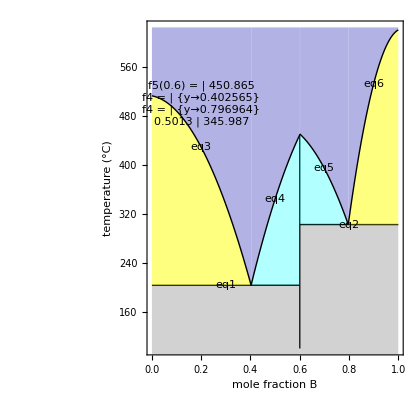

```mathematica
Module[{eqlabels,eq1,eq2,eq3,eq4,eq5,eq6,shell},
eqlabels=Graphics[{Text[Style["eq1",Background->White],{0.3,eq1}],Text[Style["eq2",Background->White],{0.8,eq2}],Text[Style["eq3",Background->White],{0.2,-1722.2*0.2^2-75.783*0.2+513.11}],Text[Style["eq4",Background->White],{0.5,-2008.9*0.5^2+3258.9*0.5-782.86}],Text[Style["eq5",Background->White],{0.7,-1929*0.7^2+1942.5*0.7-20.195}],Text[Style["eq6",Background->White],{0.9,-6655.1*0.9^2+13526*0.9-6250}]}];

eq1=203.5;
eq2=302.7;
eq3[xp_]=-1722.2*xp^2-75.783*xp+513.11;
eq4[xp_]=-2008.9*xp^2+3258.9*xp-782.86;
eq5[xp_]=-1929*xp^2+1942.5*xp-20.195;
eq6[xp_]=-6655.1*xp^2+13526*xp-6250;

shell=Show[
Plot[Piecewise[{{-1722.2*x^2-75.783*x+513.11,0≤x≤0.403},{-2008.9*x^2+3258.9*x-782.86,0.403≤x≤0.601},{-1929*x^2+1942.5*x-20.195,0.6≤x≤0.797},{-6655.1*x^2+13526*x-6250,0.797≤x≤1}}],{x,0,1},PlotStyle->None,Filling->Top,FillingStyle->Directive[Darker[Blue],Opacity[0.3]],PlotRange->{{0,1},{100,625}}],
Plot[203.5,{x,0,0.6},PlotStyle->{Black,Thick},Filling->Bottom,FillingStyle->Directive[Gray,Opacity[0.35]]],
Plot[302.7,{x,0.6,1},PlotStyle->{Black,Thick},Filling->Bottom,FillingStyle->Directive[Gray,Opacity[0.35]]],
Plot[-1722.2*x^2-75.783*x+513.11,{x,0,0.403},PlotStyle->{Black,Thick},Filling->203.5,FillingStyle->Directive[Yellow,Opacity[0.5]]],Plot[-2008.9*x^2+3258.9*x-782.86,{x,0.403,0.6},PlotStyle->{Black,Thick},Filling->203.5,FillingStyle->Directive[Cyan,Opacity[0.3]]],
Plot[-1929*x^2+1942.5*x-20.195,{x,0.6,0.797},PlotStyle->{Black,Thick},Filling->302.7,FillingStyle->Directive[Cyan,Opacity[0.3]]],
Plot[-6655.1*x^2+13526*x-6250,{x,0.797,1},PlotStyle->{Black,Thick},Filling->302.7,FillingStyle->Directive[Yellow,Opacity[0.5]]],
Graphics[{{Thick,Black,Line[{{0.6,100},{0.6,450.377}}]},Text[Framed[Grid[{
{"f5(0.6) =",eq5[0.6]},{"f4 =",FindRoot[eq4[y]==eq1,{y,0.1}]},{"f4 =",FindRoot[eq5[y]==eq2,{y,0.6}]},
{0.5*(0.4026+0.6),eq4[0.5*(0.4026+0.6)]}
}],Background->White],{0.2,500}]}],eqlabels,AspectRatio->1,ImageSize->420,Frame->True,FrameLabel->{"mole fraction B","temperature (°C)"},FrameStyle->14]
]
```

```mathematica
N[3.19*ⅇ-767-1.93*ⅇ]
```

-763.575

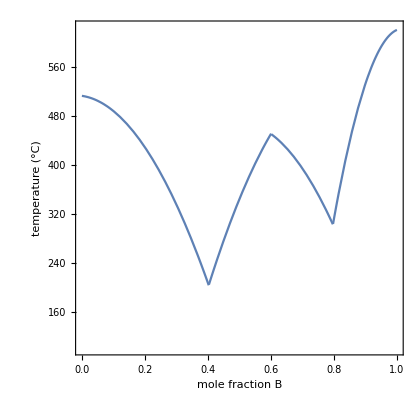

```mathematica
shell=Show[
Plot[Piecewise[{
{-1722.2*x^2-75.783*x+513.11,0≤x≤0.403},
{-1930*x^2+3188*x-767.3,0.403≤x≤0.601},
{-1929*x^2+1942.5*x-20.195,0.6≤x≤0.797},
{-6655.1*x^2+13526*x-6250,0.797≤x≤1}}],{x,0,1},FillingStyle->Directive[Darker[Blue],Opacity[0.3]],PlotRange->{{0,1},{100,625}}],AspectRatio->1,ImageSize->420,Frame->True,FrameLabel->{"mole fraction B","temperature (°C)"},FrameStyle->14]
```

```mathematica
Solve[{
203.5==a*(0.4026)^2+b*0.4026+c,
346==a*(0.5013)^2+b*0.5013+c,
450.9==a*(0.6)^2+b*0.6+c},{a,b,c}]
```

{{a→-1929.85,b→3188.16,c→-767.25}}

```mathematica
x1=Solve[-1930*x^2+3188*x-767.3==-1722.2*x^2-75.783*x+513.11,x]

x2=Solve[-1930*x^2+3188*x-767.3==-1929*x^2+1942.5*x-20.195,x]
```

{{x→0.40263},{x→15.3037}}

{{x→0.600133},{x→1244.9}}

```mathematica
x=0.6;
-1930*x^2+3188*x-767.3
-1929*x^2+1942.5*x-20.195
```

450.7

450.865